# Non-Linear Resonance

#### The objectives of the present notebook are: 1) Reviewing the theory underlying non-linear resonance. 2) Identifying the relevant parameters for interpreting resonance in the Chua’s Circuit system.

** The present notebook review non-linear resonance with classical axiomatic principles and does not adventure into the quantum interpretation of dynamical systems.

## 1. Dynamical Systems

#### How are dynamical systems mathematically formulated? What variables are utilized in order to describe their dynamics?

#### Variable Definitions

```mathematica
δ = 0.00; (*Damping Constant*)
ω0 = 0.00; (*Natural Frequency*)
 Α = 0.00; (*Amplitude*)
β = 0.00 ;(*Experimental Constant*)
Ρ = 0.00;  (*Phase*)
λ = 0.00; (*Damping Decay Rate*)

ϝ= ω0 / 2*Pi; (*Number of cycles / time unit = Hertz*)
τ = 1 / λ; (*Time constant = The time necessary for A to decrease by a factor of E (Euler's Number)*)
ϛ = λ / Sqrt[λ^2 + ω0^2]; (*Damping Ratio = Relation between the rate of decay and the natural frequency*)
𝒬 = 1 / (2 * ϛ); (*Q Factor = Representation of the amount of damping. High Q is interpreted as slow damping relative to the oscillation.*)
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

#### Natural Frequency ω0

The natural frequency of a system describe the oscillating behavior exhibited internally by a dynamical system.

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ ω0*x[t] == 0,

(*Initial Conditions*)
x[0] == 1, 
x'[0] == 0},

x[t],

{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{ω0, 0,"Natural Frequency ω0"},0, 5}]
```

As you can observe, increasing the natural frequency of our pendulum will result to an increase in the number of cycle per unit of time. As no damping term is present within the equation, the oscillations do not decay overtime.

#### Damping δ

Damping describe the decay of oscillation amplitude over time. 

Relating to the natural frequency with damping:

δ = 0 --> Undamped System
δ < ω0 --> Underdamped System
δ = ω0 --> Critically Damped System
δ > ω0 --> Overdamped

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+δ*x'[t]+ ω0*x[t] == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{ω0,0,"Natural Frequency -> ω0"},5.00, 15.00},
{{δ, 0,"Underdamped -> (δ < ω0)"},0.01, 3.99},
{{δ, 0,"Critically Damped -> (δ = ω0)"},5.00, 15.00},
{{δ, 0,"Over Damped -> (δ > ω0)"}, 15.01,50.00}]
```

RATE λ of DECAY:

```mathematica
Manipulate[

Plot[
{Α*E^(-λ*t)*Cos[ω0*t+Ρ]},
{t, 0, 10},
PlotRange->All,
PlotStyle->Red],

{{Α,0,"Amplitude -> Α"},0.00, 1.00},
{{ω0, 0,"Frequency -> ω0"},0.00, 50.00},
{{Ρ, 0,"Phase -> Ρ "},0.00, 5.00},
{{λ, 0,"Decay Rate -> λ "},0.00, 5.00}]
```

The DAMPING RATIO appears as a commonly used parameters describing the damping behavior exhibited by a system :
      
ζ = 0 -- > Undamped (Oscillations occur indefinitely with a constant amplitude over time)
ζ < 1 -- > Underdamped (Oscillations slowly decrease over time where the system is found to exhibit overshoot behavior until equilibrium is reached.)
ζ = 1 -- > Critically damped (
ζ > 1 -- > Overdamped (Oscillations rapidly decrease and eventually reach a rest position without ever over shooting. Note that the complete absence of oscillation is a fundamental limit of quantum mechanics. Nature appears to be incapable of reaching such as state where dynamical oscillations are absent.)

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+(2*ϛ*ω0)*x'[t]+ ω0^2*x[t] == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{ω0,0,"Natural Frequency -> ω0"},0.00, 15.00},
{{ϛ, 0,"Underdamped -> ϛ < 1"},0.00, 0.99},
{{ϛ, 0,"Critically Damped -> ϛ = 1"},1.00, 1.00},
{{ϛ, 0,"Over Damped -> ϛ > 1"},1.001, 5.00}]
```

Increasing the amount of damping within the system will consequently leads to an incremental decrease of the natural frequency amplitude over time. 

Experimental example of damping (δ):
- Viscous Drag.
- Heat Dissipation.

#### Oscillating Spring Example

```mathematica
κ  = 0.00; (*Experimental stifness constant of the spring*)
𝓂 = 0.00; (*Mass value attached to the end of the spring*)
```

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+(κ/𝓂)*x[t] == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{κ , 1, 5},
{𝓂 , 1, 10}]
```

As expected, the frequency of oscillation becomes lower as the mass value associated with the object attached to the spring becomes larger than the stiffness constant. Oppositely, if the mass of the object is very small compared with the stiffness constant, the frequency of oscillation is increase dramatically. 

The present example demonstrate how the natural frequency of a system can be adjusted experimentally. For the present case, the selection of an object with a specific mass as well as a spring with a desired stiffness constant will leads to a predictable natural frequency. As you might expect, a damping term would need to be added in order to represent a realistic version of an experiment. If no external energy is provided to the oscillating spring, the oscillation frequency will slowly decay over time.

### Having now gained some perspectives on how dynamical systems are mathematically represented, you can imagine the possibilities of observing various types of oscillator systems. We will explore below some known oscillator systems with peculiar properties.

#### Pendulum Oscillator

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+δ*x'[t] + Sin[x[t]] == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{δ, 0, 5}]
```

#### Pendulum Oscillator Potential Energy

```mathematica
Clear[x]
```

```mathematica
Manipulate[

Plot[-Cos[x], 
{x, -5, 5},
PlotStyle->Red],
{x, -5, 5}]
```

#### Phase Space Representation (Angular Velocity (vs) Angle Position)

A phase space representation of a dynamical system allow to

```mathematica
Clear[x]
Clear[y]
```

```mathematica
v = NDSolve[

{x'[t] == 0.1*x[t]+y[t], 
y'[t] == -x[t]+0.1*y[t], 
x[0] == 0.01,
y[0] == 0}, 

{x[t], y[t]},

{t, 0, 50}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

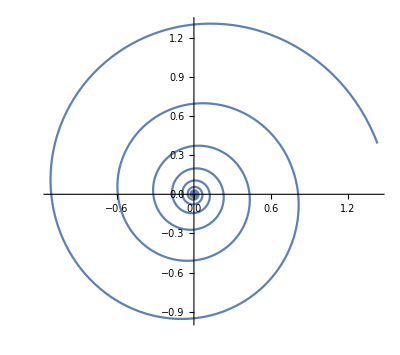

```mathematica
ParametricPlot[

{x[t], y[t]}/.v, 

{t, 0, 50}, 
PlotRange->All,
PlotPoints->1000]
```

### Van Der pol Oscillator (Non-Linear Damping)

The peculiarity of the Van Der pol Oscillator arises from the NON-LINEAR DAMPING.

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]- β*(1-x[t]^2)*x'[t]+  ω0^2*x[t] == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{β, 0, 5},
{ω0, 0, 5}]
```

### Morse Oscillator

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t] + β*E^(-x[t])*(1-E^(-x[t])) == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{δ, 0, 5},
{β, 0, 5}]
```

#### Morse Oscillator Potential Energy

```mathematica
Manipulate[

Plot[
p[x] = 1/2*β*E^(-x)*(E^(-x)-2),
{x, -1,4},
PlotStyle->Red],
{β, 0.01, 1}]
```

#### Phase Space Representation

#### Experimental Examples of Morse Oscillator

### Jerk Oscillator (Third Derivative Term)

```mathematica
Manipulate[

sol = NDSolve[
{x'''[t]+ δ *x''[t]+ β*x'[t] + ω0^2*x[t]== 0,
x[0] == 1, 
x'[0] == 0,
x''[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{δ, 1, 5},
{β, 1, 5},
{ω0, 1, 5}]
```

#### Jerk Oscillator Potential Energy

#### Phase Space Representation

#### Experimental Examples of Jerk Oscillator

### Duffin Oscillator

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*x[t] + β*x[t]^3 == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{δ, 0, 5},
{ω0, 0, 5},
{β, 0, 5}]
```

#### Duffin Oscillator Potential Energy

```mathematica
Manipulate[

Plot[
p[x] = 1/2*ω0^2*x^2+1/4*β*x^4,
{x, -5,5},
PlotStyle->Red],

{ω0, -5,5},
{β, -5, 5}]
```

#### Phase Space Representation

#### Experimental Examples of Duffin Oscillators

### Quintic Oscillator

```mathematica
ν = 0.00;
```

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*x[t] + β*x[t]^3 + ν*x[t]^5== 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{δ, 0, 5},
{ω0, 0, 5},
{β, 0, 5},
{ν, 0, 5}]
```

#### Quintic Oscillator Potential Energy

```mathematica
Manipulate[

Plot[
p[x] = 1/2*ω0^2*x^2+1/4*β*x^4+ 1/6*ν*x^6,
{x, -5,5},
PlotStyle->Red],

{ω0, -5,5},
{β, -5, 5},
{ν, -5, 5}]
```

#### Phase Space Representation

#### Experimental Examples of Quintic Oscillators

## 2. External Forces & Resonant Responses

#### How are external forces mathematically formulated?

Oscillator Variables Definition:

```mathematica
δ = 0.00; (* Damping Constant *)
ω0 = 0.00; (* Natural Frequency *)
β = 0.00 ;(* Experimental Constant *)
 Α = 0.00; (*Amplitude*)
```

Force Variables Definition:

```mathematica
ωf = 0.00; (* Applied Force Frequency *)
af = 0.00 ;(* Applied Force Amplitude *)
```

#### Frequency Response Analysis

```mathematica
S = (ω0^2 - ωf^2)^2+ δ^2*ωf^2; 

Q = 1 / Sqrt[S]; (*Response Amplitude - Also defined as:  Q= Α/ωf*)

ωfMax= Sqrt[ω0^2-(δ^2/2)]; (*wfMax = Force frequency inducing a maximum response by the system*)

freqForceMax[ω0_, δ_]:= Sqrt[ω0^2-(δ^2/2)] (*Function allowing to derive the force frequency inducing a maximum amplitude response*)
```

Frequency Response Curve Example:

```mathematica
Clear[ω0, ωf, δ]
```

```mathematica
Manipulate[

Plot[
1 / Sqrt[(ω0^2 - ωf^2)^2+ δ^2*ωf^2],
{ωf, 0, 3},
PlotRange->All,
PlotStyle->Red,
AxesLabel-> {"Force Frequency ωf", "Amplitude Response Q"}],

{{δ,0,"Damping -> δ"},0.00, 3.0},
{{ω0,1,"Natural Frequency -> ω0 = 1"},1.00, 1.00}]
```

The frequency response curve below demonstrate the effect of damping on the response amplitude. 

Beyond a certain threshold of damping value, resonance becomes impossible. Specifically:

- δ > Sqrt[2*ω0^2] --> NO RESONANCE
- δ < Sqrt[2*ω0^2] --> RESONANCE BECOMES POSSIBLE
- Force Frequency inducing a maximum response amplitude = Sqrt[ω0^2-(δ^2/2)]

As shown below, as damping value increases, the required force frequency to induce a maximum amplitude decreases.

```mathematica
Manipulate[
freqForceMax[1, Damping],
{Damping, 0, 0.5}]
```

#### Resonance in Duffing Oscillator System

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*x[t] + β*x[t]^3 == af*Cos[ωf*t],
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{δ, 0,"Damping -> δ "},0, 5},
{{ω0, 0,"Natural Frequency -> ω0"},0, 5},
{{β, 0,"Stiffness Constant -> β "},0,  5},
{{af, 0,"Force Amplitude -> af "},0,  5},
{{ωf, 0,"Force Frequency -> ωf "},0,  5}]
```

## 3. Stochastic Resonance

#### Noise is intuitively assumed to distract and interfere when accuracy is required. However, stochastic resonance demonstrate the contrary. Yet, when noise intensity provided from the environment reaches a specific threshold upon a bi-stable system, the signal-to-noise ratio measured at the input frequency W becomes maximized, and the system jumps periodically from one potential to another.

#### Stochastic Resonance in Duffing Oscillator

Duffing Potential

```mathematica
Manipulate[

Plot[
1/2*ω0^2*x^2+1/4*β*x^4,
{x, -2, 2}],

{{ω0, -1,"Natural Frequency --> ω0"}, -5, 5},
{{β, -0.5,"Stiffness --> β"}, -2, 2}]
```

As demonstrated in the above simulation, when the noise value crosses a threshold, the system is forced to oscillate from one potential well to another.

## 4. Vibrational Resonance

#### As opposed to stochastic resonance, vibrational resonance does not require a bistable system to induce a maximum response. The noise term is replaced by a high-frequency force that allows the system to transition from stability and adventure widely in the phase space. Such transition induced by a high-frequency force is often associated with a maximum response by excitable systems such as biological tissues.

#### Vibrational Resonance in Duffing Oscillator

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*x[t] + β*x[t]^3 == af*Cos[ωfa*t] + bf* Cos[ωfb*t],
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red,
AxesLabel-> {"Time (Sec)", "State x(t)"}],

{{δ, 0,"Damping -> δ "},0, 5},
{{ω0, 0,"Natural Frequency -> ω0"},0, 5},
{{β, 0,"Stiffness Constant -> β "},0,  5},

(*External Force Parameters*)

{{af, 0,"Force Amplitude A-> af "},0,  5},
{{bf, 0,"Force Amplitude B-> bf "},0,  5},
{{ωfa, 0,"Force Frequency A -> ωfa "},0,  5},
{{ωfb, 0,"Force Frequency B -> ωfb "},0,  5}]
```

## 5. Coherence Resonance

#### Coherence resonance share similarity with stochastic resonance. The addition of a small noise intensity reaching a specific threshold induces a maximum amplitude response by the system. However, contrarily to stochastic resonance, coherence resonance does not require a periodic force. Specifically, noise only can induce temporal order in the dynamics of a coherent oscillator.

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*x[t] + β*x[t]^3 == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red,
AxesLabel-> {"Time (Sec)", "State x(t)"}],

{{δ, 0,"Damping -> δ "},0, 5},
{{ω0, 0,"Natural Frequency -> ω0"},0, 5},
{{β, 0,"Stiffness Constant -> β "},0,  5},

(*External Force Parameters*)

{{af, 0,"Force Amplitude A-> af "},0,  5},
{{bf, 0,"Force Amplitude B-> bf "},0,  5},
{{ωfa, 0,"Force Frequency A -> ωfa "},0,  5},
{{ωfb, 0,"Force Frequency B -> ωfb "},0,  5}]
```

## 6. Ghost Resonance

#### What if the principles underlying stochastic and vibrational resonance are combined? Surprisingly, the combination of two periodic forces paired with a noise intensity at a specific threshold induces a maximum response in a system at a frequency missing from the input driving force. If the noise intensity is increased beyond the ghost resonant threshold, resonance at a frequency matching the input arises. Ghost frequency response can be triggered by either a noise intensity (ghost-stochastic resonance) or a high-frequency force (ghost-vibrational resonance).

#### Vibrational Ghost Resonance in Duffing Oscillator System

```mathematica
δ = 0.00; (*Damping Constant*)
ω0 = 0.00; (*Natural Frequency*)
 Α = 0.00; (*Amplitude*)
β = 0.00 ;(*Experimental Constant*)
Ρ = 0.00;  (*Phase*)
λ = 0.00; (*Damping Decay Rate*)

ωf = 0.00; (* Applied Force Frequency *)
af = 0.00 (* Applied Force Amplitude *)

fi = (k+n-1)*ωf1;
F = (af1/n) Sum[Sin[2*Pi*fi*t], {1, n}];
```

0.

Sum::itraw: Raw object 1 cannot be used as an iterator.

Sum::vloc: The variable 1 cannot be localized so that it can be assigned to numerical values.

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+a * x[t]+β*x[t]^3 == F+  af2*Cos[ωf2*t],
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

(*System's Parameters*)
{{δ, 1,"Damping -> δ "},1, 50},
{{a, 1,"Experimental Variable -> a"},1, 50},
{{β, 1,"Experimental Variable -> β "},1,  50},

(*External Forces*)
{{af1, 1," Force Amplitude 1 -> af1 "},1,  50},
{{n, 1," Number of Periodic Forces  -> n "},1,  50},
{{k, 1," Positive Integer -> k "},1,  50},
{{ωf1, 1," Force 1 Frequency -> ωf1 "},1,  50},

(*High-Frequency Force*)
{{af2, 1," Force Amplitude 2 -> af2 "},1,  50},
{{ωf2, 1," Force 2 Frequency -> wf2 "},1,  50}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{x[t]+x[t]^3+x'[t]+x''[t]==F+Cos[t],x[0]==1,x'[0]==0},x[t],{t,0,1000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x[0.00204286]+x[0.00204286]^3+x'[0.00204286]+x''[0.00204286]==0.999998+F,x[0]==1,x'[0]==0},x[0.00204286],{0.00204286,0,1000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x[0.00204286]+x[0.00204286]^3+x'[0.00204286]+x''[0.00204286]==0.999998+F,x[0.]==1.,x'[0.]==0.},x[0.00204286],{0.00204286,0.,1000.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{x[t]+x[t]^3+x'[t]+x''[t]==F+Cos[t],x[0]==1,x'[0]==0},x[t],{t,0,1000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x[0.00204286]+x[0.00204286]^3+x'[0.00204286]+x''[0.00204286]==0.999998+F,x[0]==1,x'[0]==0},x[0.00204286],{0.00204286,0,1000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x[0.00204286]+x[0.00204286]^3+x'[0.00204286]+x''[0.00204286]==0.999998+F,x[0.]==1.,x'[0.]==0.},x[0.00204286],{0.00204286,0.,1000.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

## 7. Parametric Resonance

#### The characteristic of parametric resonance is fundamentally different from other resonances where the oscillator responds to periodic external stimuli. A maximum amplitude response arises when one or more system parameters change periodically over time. For instance, a system with a natural frequency exhibiting periodic change will have a maximum amplitude response when the rate of change reaches a specific threshold. Parametric resonance can also occur from the periodicity of other parameters such as stiffness, damping, density, etc. Systems capable of exhibiting parametric resonance are referred to as parametric oscillators. Different types of resonances arise based on the range of values taken by the system and forces parameters. Note that the present examples are only a small portion of the possible resonances nature has to offer. Additionally, the present notebooks only interpret classical oscillators and do not adventure into oscillators that require a quantum description. A wide range of phenomena becomes possible when resonance is interpreted with principles offered by quantum mechanics.

#### Parametric Resonance in Duffing Oscillator System

```mathematica
Clear[δ , ω0, Α]
```

```mathematica
δ = 0.00; (*Damping Constant*)
ω0 = 0.00; (*Natural Frequency*)
 Α = 0.00; (*Amplitude*)
ωf = 0.00 ;(*Periodic Frequency*)
(*Damping Decay Rate*)
```

```mathematica
Manipulate[

sol = NDSolve[
(*The natural frequency of the pendulum is no longer constant*)
{x''[t]+ δ*x'[t]+ β*x[t]^3+ Α*x[t]*Sin[ωf*t]== 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red,
AxesLabel-> {"Time (Sec)", "State x(t)}"}],

{{δ, 0.1,"Damping -> δ "},0.1, 50},
{{ω0, 0,"Natural Frequency -> ω0"},0, 50},
{{ Α, 1,"Amplitude Parameter ->  Α "},1,  50},
{{ωf, 0,"Frequency Parameter -> ωf "},0,  50},
{{β, 0,"Experimental Constant -> β "},0,  50}]
```

```mathematica
Manipulate[

sol = NDSolve[
(*The natural frequency of the pendulum is no longer constant*)
{x''[t]+ δ*x'[t]+ω0^2*(1+ Α*Cos[ωf*t])*Sin[x[t]]== 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{δ, 0.1,"Damping -> δ "},0.1, 50},
{{ω0, 0,"Natural Frequency -> ω0"},0, 50},
{{ Α, 1,"Amplitude Parameter ->  Α "},1,  50},
{{ωf, 0,"Frequency Parameter -> ωf "},0,  50}]
```

## 8. Auto-Resonance

Auto-resonance arises from an external driving force having a frequency that is changing non-linearly over time. The excited non-linear system undergo a phase locking behavior where the oscillation of the system becomes govern by the evolving force frequency. As a result, auto-resonance phenomenon allows the excitation of non-linear system to extremely high energy. Surprisingly, the phase-locking mechanisms underlying auto-resonance occurs even when the parameters of the systems are varied over time. In fact, parametric auto-resonance is possible where one or more parameters of the systems become dependent on the driving force. Naturally, one may wonder about the possibility of observing phase-locked systems at a distance ...

#### Auto - Resonance in the Pendulum System

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*Sin[x[t]] == af*Cos[(ω0*t - a*t^2)/2] ,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 2000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 2000},
PlotRange->All,
PlotStyle->Red,
AxesLabel-> {"Time (Sec)", "State x(t)"}],

{{δ, 0.01,"Damping -> δ "},0, 0},
{{ω0, 0.5,"Natural Frequency -> ω0"},0, 1},

(*External Force Parameters*)

{{af, 0.0461,"Force Amplitude af-> af "},0,  0.05},
{{a, 0.001,"Frequency Sweet/Shirp Rate a-> a "},0,  0.001}]
```

Adjusting the frequency of the external force clearly demonstrate specific thresholds upon which the amplitude of the system keeps increasing over time.

#### Parametric Auto-resonance using the Duffing Oscillator

External auto-resonance 

Consider the example of a child swinging on a pendulum. If an external push is applied once every period in order to increase the amplitude of oscillation, the time interval between each push will increases as the amplitude of the pendulum grows. In order words, the child swinging with a higher amplitude will take more time to return to the pushing site. 


Parametric auto-resonance

 Contrarily to the previous example where auto-resonance is induced externally, parametric auto-resonance occurs as a result of a changing internal parameter. For instance, imagine a child swinging on a pendulum where the growth of swinging amplitude no longer depends on an external applied force but on the variation of its center of gravity. Specifically, a child moving his center-of-mass twice in each oscillation cycle will allow to produce a similar growth amplitude as described with external auto-resonance. As amplitude of oscillation grows, the child will move his center-of-mass with an increasing time interval. The present example involve a child varying its center-of-mass, but imagine an ions in a medium with a constantly changing center of mass. Any oscillating charges must consequently be paired with the propagation of electromagnetic-wave throughout the surrounding environment. One may therefore wonder whether parametric auto-resonance occurring as a result of system’s parameter changing over time can leads to non-local phase locking mechanisms. In other words, the interval ionic oscillation undergoing parametric auto-resonance leads to the emission of electromagnetic wave having a signature capable of phase-locking the oscillation of another systems located at high distances. Investigating the space-time properties of auto-resonance phenomenon may allow the observation of interesting non-local phenomenon.

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*x[t] + af*x[t]*Cos[a*t] +  β*x[t]^3== 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red,
AxesLabel-> {"Time (Sec)", "State x(t)"}],

{{δ, 0,"Damping -> δ "},0, 5},
{{ω0, 0,"Natural Frequency -> ω0"},0, 5},
{{β, 0,"Stiffness Constant -> β "},0,  5},
{{af, 0,"Varying Amplitude -> af "},0,  5},
{{a, 0,"Chirp Rate -> a "},0,  5}]
```

The same growth amplitude observed previously in the external pendulum can be observed. However, no external forces are acting on the system. The system’s parameters only allows to induce a resonance action where the amplitude of oscillation grows indefinitely over time.

## 9. Chua’s Circuit as a Non-Linear Oscillator

The parameters can be divided into two categories. A set of parameters describing the circuit’s behaviour (system) and a set of parameters describing the external input signal.

The system’s parameters can be categorized based on three requirements attributed to chaos in electronic circuits:

1) One or more non-linear elements --> Chua’s Diode composed of:

Operational Amplifiers

The values of parameters M0 and M1 arises from different schematic configuration and become crucially important in describing the non-linear property of the circuit.

2) One or more locally active resistors (Negative resistance within Chua’s Diode sub-circuit):

Resistors R1, R2, R3, R4, R5, R6

3) Three or more energy storage elements:

Inductor L1

Capacitor C1

Capacitor C2

Taken together, the dynamical state of the circuit becomes describable with only three variables:

- Voltage Across Capacitor C1 = (V1) or (X)

- Voltage Across Capacitor C2 = (V1) or (Y)

- Current Across Inductor L1 = (I) or (Z)

*** The provided simulation below was gathered from -->  https : // demonstrations.wolfram.com/SimplestChaoticCircuit/

```mathematica
Manipulate[
Module[{
sol={v,i,x}/.Quiet[NDSolve[{

v'[t]==i[t]/CC,

i'[t]==-1/L(v[t]+
Switch[memristanceChoices,

1,β( x[t]^2 -1),
2,-β x[t],
3,β x[t]]*i[t]),

x'[t]==Switch[internalStateChoices,

1,-i[t]-α x[t]+i[t]*x[t],
2,1-i[t]^2,
3,2/7 i[t]-3/14(Abs[i[t]+1]-Abs[i[t]-1])],

v[0]==v0,
i[0]==i0,
x[0]==x0},

{v,i,x},
{t,0,tmax},
MaxSteps->Infinity]][[1]]},

Grid[{{Text@Style["2D phase portrait, time domain waveform, and a 3D phase portrait",Bold],SpanFromLeft,SpanFromLeft},
{ParametricPlot[{First[sol][t],First[Rest[sol]][t]},{t,0,tmax},AxesLabel->{v[t],i[t]},ImageSize->{180,180},AspectRatio->1,PlotRange->All,MaxRecursion->8,PerformanceGoal->8,ImagePadding->25],Plot[First[sol][t],{t,0,tmax},AxesLabel->{t,v[t]},ImageSize->{150,150},PlotRange->All,MaxRecursion->8,PerformanceGoal->8,ImagePadding->20]},
{ParametricPlot3D[{First[sol][t],First[Rest[sol]][t],Last[sol][t]},{t,0,tmax},AxesLabel->{v,i,x},ImageSize->{180,180},BoxRatios->{1,1,1},PlotRange->Full,MaxRecursion->8,PerformanceGoal->8,ColorFunction->"Rainbow",ImagePadding->20],SpanFromLeft}}]],Style["system parameters",Bold],

(* Memristance and Internal State Functions *)
{{memristanceChoices, 1, "memristance"},{
1->"β (x^2 - 1)",
2->"- β x",
3->"β x"},
ControlType->PopupMenu,
ControlPlacement->Top},

{{internalStateChoices, 1, "internal state function"},{
1->"- i - α x + i x",
2->"1 - i^2",
3->"2/7 i - 3/14 (|i + 1} - |i - 1})"},
ControlType->PopupMenu,
ControlPlacement->Top},


{{β,1.5,"β"},1,3,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{α,0.6,"α"},0.1,3,0.1,Enabled:>memristanceChoices===1,Appearance->"Labeled",ImageSize->Tiny},

(* Circuit Parameters and Simulation Time *)
{{CC,1,"C"},1,3,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{L,3,"L"},1,5,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{tmax,500,"t"},0.1,1000,0.1,Appearance->"Labeled",ImageSize->Tiny},

(* Initial Conditions *)
{{v0,0.1,"v_0"},-1,1,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{i0,0,"i_0"},-1,1,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{x0,0.1,"x_0"},-1,1,0.1,Appearance->"Labeled",ImageSize->Tiny},
SynchronousUpdating->False,ControlPlacement->Left,AutorunSequencing->{1,3,5,7},TrackedSymbols->True]
```